# Neural Logic

```mathematica
Get["neural-logic.m",Path->NotebookDirectory[]];
```

```mathematica
?neurallogic`*
```

## Utilities

```mathematica
HardPrediction[m_]:=Ordering[(With[{t=#[True]},If[MissingQ[t],0,t]]&)/@Counts/@m,-1]
HardTarget[t_]:=Flatten[Position[t,True]]
HardResults[hardPredictionTargetPairs_]:=Module[{results,accuracy},
results=Reverse[Sort[Counts[{HardPrediction[First[#]][[1]],HardTarget[Last[#]][[1]]}&/@hardPredictionTargetPairs]]];
accuracy=KeySelect[results,First[#]==Last[#]&];
{"Accuracy = "<>ToString[Total[accuracy]/Length[hardPredictionTargetPairs]*100.0]<>"%",results}
]
```

## Learn XOR

## Generate training data

```mathematica
numBooleanVariables=25;
Echo[2^numBooleanVariables];
bf=BooleanConvert[Xor[#1,#2,#3,#4,#5,#6,#7,#8,#9,#10,#11,#12,#13,#14,#15,#16,#17,#18,#19,#20,#21,#22,#23,#24,#25]&,"BooleanFunction"];
maxExamples=10000;
numClasses=2;
examples=Map[With[{x=RandomChoice[{0,1},numBooleanVariables]},Soften/@x->Soften[Boole[With[{r=bf@@x},{r,!r}]]]]&,Range[maxExamples]];
{trainData,testData}=[examples,"TestSetSize"->Scaled[0.2],"Shuffle"->True];
```

33554432

## Hard neural logic

### Create net

```mathematica
inputSize=Length[First[First[trainData]]];
```

```mathematica
{net,hardNet}=With[{classificationLayerSize=4*numClasses},
HardNeuralChain[{
HardNeuralNOR[inputSize,200],
HardNeuralNOR[200,classificationLayerSize],
HardNeuralPortLayer[classificationLayerSize,numClasses]
}]];
```

```mathematica
{net,hardNet}=With[{classificationLayerSize=4*numClasses},
HardNeuralChain[{
HardNeuralMajority[inputSize,200],
HardNeuralMajority[200,classificationLayerSize],
HardNeuralPortLayer[classificationLayerSize,numClasses]
}]];
```

```mathematica
softNet=AppendHardClassificationLoss[net]
```

NetGraph[<>]

### Train net

```mathematica
{trainedNet,resultsObject}=NetTrain[softNet,trainData,{"TrainedNet","ResultsObject"},
ValidationSet->{RandomSample[testData,UpTo[1000]],"Interval"->10},
LossFunction->"Loss",
Method->{"ADAM"},
TargetDevice->"GPU",
MaxTrainingRounds->20000];
```

```mathematica
trainedSoftNet=NetExtract[trainedNet,"NeuralLogicNet"]
```

NetChain[<>]

### Evaluate soft net

```mathematica
resultsObject["RoundMeasurements"]
softPredictionTargetPairs=[{trainedSoftNet[First[#]],Last[#]}&,testData];
hardenedPredictionTargetPairs=Harden[softPredictionTargetPairs];
MatrixForm/@Flatten[RandomSample[hardenedPredictionTargetPairs,5],1]/.{True->Style[True,Red]};
Column[HardResults[hardenedPredictionTargetPairs]]
```

<|Loss→0.249198|>

{(False | True | True | False
False | False | False | True),(True
False),(False | True | True | False
True | True | False | True),(False
True),(False | True | True | False
True | False | False | True),(False
True),(False | True | True | False
False | False | False | True),(False
True),(False | False | True | False
False | True | False | True),(False
True)}

Accuracy = 49.75%
<|{2,2}→586,{2,1}→565,{1,2}→440,{1,1}→409|>

### Evaluate hard net

```mathematica
hnf=HardNetFunction[hardNet,trainedSoftNet];
hardPredictionTargetPairs=[{hnf[Harden[First[#]]],Last[#]}&,testData];
Column[HardResults[hardenedPredictionTargetPairs]]
```

Accuracy = 49.75%
<|{2,2}→586,{2,1}→565,{1,2}→440,{1,1}→409|>

```mathematica
SpaceSaving[trainedSoftNet]
```

Soft net size = 27.232 kilobytes
Hard net size = 0.851 kilobytes
Saving factor = 32.

## Learn MNIST

## Generate training data

```mathematica
ConvertBinaryStringToList[s_String]:=ToExpression["{"<>StringInsert[s,",",Drop[Range[StringLength[s]],1]]<>"}"]
ConvertBinaryStringToImageData[s_String,{width_,height_}]:=ArrayReshape[ConvertBinaryStringToList[s],{width,height}]
MNISTExample[example_]:=(Soften/@ConvertBinaryStringToList[First[example]])->Last[example]
MNISTImageExample[example_,w_,h_]:=Image[ConvertBinaryStringToImageData[First[example],{w,h}],ImageSize->Tiny]->Last[example]
TargetClass[class_,numClasses_]:=Table[If[i==ToExpression[class]+1,1,0],{i,1,numClasses}]
```

```mathematica
first2Digits=12665;
first4Digits=24754;
data=Flatten[StringSplit/@Take[Import[FileNameJoin[{NotebookDirectory[],"data/mnist_data.csv"}]],first4Digits],1];
numClasses=Length[DeleteDuplicates[Last/@data]];
data=Map[First[#]->TargetClass[Last[#],numClasses]&,data];
```

```mathematica
MNISTImageExample[#,8,8]&/@RandomSample[data,8]
```

{-Graphics-→{0,1,0,0},-Graphics-→{1,0,0,0},-Graphics-→{0,0,1,0},-Graphics-→{0,0,1,0},-Graphics-→{1,0,0,0},-Graphics-→{1,0,0,0},-Graphics-→{0,0,0,1},-Graphics-→{0,1,0,0}}

```mathematica
{trainData,testData}=[MNISTExample/@data,"TestSetSize"->Scaled[0.8],"Shuffle"->True];
```

## Standard neural net

```mathematica
ConvertDataToClasses[data_]:=MapAt[First[Flatten[Position[#,1]]]-1&,data,{All,2}]
```

### Create net

```mathematica
net=With[{classificationLayerSize=numClasses},
NetChain[{
300,LogisticSigmoid,
classificationLayerSize,LogisticSigmoid,
SoftmaxLayer[]
},
"Output"->NetDecoder[{"Class",{"0","1","2","3"}}]
]];
```

### Train net

```mathematica
result=NetTrain[net,ConvertDataToClasses[trainData],All,
ValidationSet->{ConvertDataToClasses[RandomSample[testData,UpTo[1000]]],"Interval"->10},
Method->{"ADAM"},
TargetDevice->"GPU",
MaxTrainingRounds->2000];
```

### Evaluate net

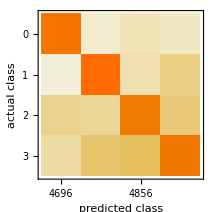
Classifier Measurements
Classifier method | Net
Number of test examples | 19803
Accuracy | (94.060.17) %
Accuracy baseline | (26.930.32) %
Geometric mean of probabilities | 0.448 ± 0.00065
Mean cross entropy | 0.803 ± 0.0014
Single evaluation time | 2.7 ms/example
Batch evaluation speed | 171. examples/ms
-Graphics- |

```mathematica
ClassifierMeasurements[result["TrainedNet"],ConvertDataToClasses[testData]]
```

```mathematica
Quantity[Length[Flatten[Normal/@Select[NetExtract[result["TrainedNet"],{All,"Weights"}],!MissingQ[#]&]]]*32.0/8000,"kilobytes"]
```

81.6 kB

## Hard neural logic

### Create net

```mathematica
{net,hardNet}=With[{classificationLayerSize=12*numClasses},
HardNeuralChain[{
HardNeuralNAND[Length[First[First[trainData]]],300],
HardNeuralNAND[300,classificationLayerSize],
HardNeuralPortLayer[classificationLayerSize,numClasses]
}]];
```

```mathematica
{net,hardNet}=With[{classificationLayerSize=12*numClasses},
HardNeuralChain[{
HardNeuralNAND[Length[First[First[trainData]]],300],
HardNeuralMajority[300,classificationLayerSize],
HardNeuralPortLayer[classificationLayerSize,numClasses]
}]];
```

```mathematica
softNet=AppendHardClassificationLoss[net]
```

NetGraph[<>]

### Train net

```mathematica
{trainedNet,resultsObject}=NetTrain[softNet,trainData,{"TrainedNet","ResultsObject"},
ValidationSet->{RandomSample[testData,UpTo[1000]],"Interval"->10},
LossFunction->"Loss",
Method->{"ADAM"},
TargetDevice->"GPU",
MaxTrainingRounds->2000];
```

```mathematica
trainedSoftNet=NetExtract[trainedNet,"NeuralLogicNet"]
```

NetChain[<>]

### Evaluate soft net

```mathematica
resultsObject["RoundMeasurements"]
softPredictionTargetPairs=[{trainedSoftNet[First[#]],Last[#]}&,testData];
hardenedPredictionTargetPairs=Harden[softPredictionTargetPairs];
MatrixForm/@Flatten[RandomSample[hardenedPredictionTargetPairs,5],1]/.{True->Style[True,Red]};
Column[HardResults[hardenedPredictionTargetPairs]]
```

<|Loss→0.0626493|>

Accuracy = 87.0474%
<|{2,2}→5187,{1,1}→4351,{4,4}→4060,{3,3}→3640,{2,3}→666,{2,4}→458,{4,3}→305,{3,4}→304,{1,3}→214,{1,4}→143,{4,1}→128,{4,2}→108,{3,1}→102,{2,1}→99,{3,2}→37,{1,2}→1|>

### Evaluate hard net

```mathematica
hnf=HardNetFunction[hardNet,trainedSoftNet];
hardPredictionTargetPairs=[{hnf[Harden[First[#]]],Last[#]}&,testData];
Column[HardResults[hardenedPredictionTargetPairs]]
```

Accuracy = 87.0474%
<|{2,2}→5187,{1,1}→4351,{4,4}→4060,{3,3}→3640,{2,3}→666,{2,4}→458,{4,3}→305,{3,4}→304,{1,3}→214,{1,4}→143,{4,1}→128,{4,2}→108,{3,1}→102,{2,1}→99,{3,2}→37,{1,2}→1|>

```mathematica
SpaceSaving[trainedSoftNet]
```

Soft net size = 135.6 kilobytes
Hard net size = 4.2375 kilobytes
Saving factor = 32.

## Approximate neural logic

### Create net

```mathematica
softNet=NetChain[{
NeuralAND[Length[First[First[trainData]]],75],
NeuralNOT[75],
NeuralAND[75,numClasses]
}];
```

```mathematica
softNet=InitializeNeuralLogicNet[softNet];
```

### Train net

```mathematica
{trainedNet,resultsObject}=NetTrain[softNet,trainData,{"TrainedNet","ResultsObject"},
ValidationSet->{RandomSample[testData,UpTo[1000]],"Interval"->10},
(*LossFunction->CrossEntropyLossLayer["Binary"],*)
LossFunction->MeanSquaredLossLayer[],
Method->{"ADAM"},
TargetDevice->"GPU",
MaxTrainingRounds->2000];
```

### Evaluate

```mathematica
resultsObject["RoundMeasurements"]
```

<|Loss→0.0804611|>

```mathematica
randomTestSample=RandomSample[testData,UpTo[200]];
softPredictionTargetPairs=[{trainedNet[First[#]],Last[#]}&,randomTestSample];
RandomSample[softPredictionTargetPairs,10]
```

{{{4.33337×10^-6,0.0894224,0.013937,2.13952×10^-8},{0,1,0,0}},{{0.450201,0.000940334,0.0058358,0.00133961},{1,0,0,0}},{{0.00388923,0.223233,0.0197837,0.944495},{0,0,0,1}},{{0.855183,0.0121957,0.0058358,0.0109512},{1,0,0,0}},{{0.015117,0.622378,1.21929×10^-7,0.0143295},{0,1,0,0}},{{0.00197673,0.54449,0.013937,0.328144},{0,1,0,0}},{{0.999999,0.0661812,0.0587838,0.0196368},{1,0,0,0}},{{0.546544,0.00542415,0.0403483,0.0173441},{1,0,0,0}},{{0.846613,0.0121957,0.010335,0.0163952},{1,0,0,0}},{{0.395582,0.236313,0.0313908,0.90628},{1,0,0,0}}}

## Notes

```mathematica
Get["neural-logic.m",Path->NotebookDirectory[]];
```

```mathematica
{softNet,hardNet}=With[{classificationLayerSize=4*numClasses},HardNeuralChain[{
HardNeuralNAND[25,200],
HardNeuralNAND[200,classificationLayerSize],
HardNeuralPortLayer[classificationLayerSize,numClasses]
}]];
```

```mathematica
softNet
```

NetChain[<>]

```mathematica
hardNet
```

HardNAND/*HardNAND/*Function[{neurallogic`Private`input$},{Partition[First[neurallogic`Private`input$],2],Last[neurallogic`Private`input$]}]

```mathematica
hardNet[{
{x1,x2},
{
{{w1,w2},{w3,w4},{w5,w6}},(* OP weights*)
{w7,w8,w9}, (* NOT weights *)
{{w10,w11,w12},{w13,w14,w15},{w16,w17,w18},{w19,w20,w21}}, (* OP weights *)
{w22,w23,w24,w25} (* NOT weights *)
}
}]
```

{{{!(w22⊻((!(w7⊻((x1||!w1)&&(x2||!w2)))||!w10)&&(!(w8⊻((x1||!w3)&&(x2||!w4)))||!w11)&&(!(w9⊻((x1||!w5)&&(x2||!w6)))||!w12))),!(w23⊻((!(w7⊻((x1||!w1)&&(x2||!w2)))||!w13)&&(!(w8⊻((x1||!w3)&&(x2||!w4)))||!w14)&&(!(w9⊻((x1||!w5)&&(x2||!w6)))||!w15)))},{!(w24⊻((!(w7⊻((x1||!w1)&&(x2||!w2)))||!w16)&&(!(w8⊻((x1||!w3)&&(x2||!w4)))||!w17)&&(!(w9⊻((x1||!w5)&&(x2||!w6)))||!w18))),!(w25⊻((!(w7⊻((x1||!w1)&&(x2||!w2)))||!w19)&&(!(w8⊻((x1||!w3)&&(x2||!w4)))||!w20)&&(!(w9⊻((x1||!w5)&&(x2||!w6)))||!w21)))}},{}}

```mathematica
Manipulate[Plot[SoftNOT[b,w],{b,0,1},PlotRange->{{0,1},{0,1}}],{w,0,1}]
```

```mathematica
BooleanFunction[{{True,True}->True,{True,False}->True,{False,True}->False,{False,False}->True},{b,w}]
```

b||!w

```mathematica
BooleanFunction[{{True,True}->True,{True,False}->False,{False,True}->False,{False,False}->False},{b,w}]
```

b&&w

```mathematica
BooleanFunction[{{True,True}->True,{False,True}->False,{True,False}->False,{False,False}->True},{b,w}]//Simplify
```

!(b⊻w)

```mathematica
{softNet,hardNet}=HardNeuralAND[2,4];
```

```mathematica
hn=hardNet[{b1,b2,b3},{{w1,w2,w3},{w4,w5,w6},{w7,w8,w9},{w10,w11,w12},{w13,w14,w15}}]
```

{(b1||!w1)&&(b2||!w2)&&(b3||!w3),(b1||!w4)&&(b2||!w5)&&(b3||!w6),(b1||!w7)&&(b2||!w8)&&(b3||!w9),(b1||!w10)&&(b2||!w11)&&(b3||!w12),(b1||!w13)&&(b2||!w14)&&(b3||!w15)}

```mathematica
{softNet,hardNet}=HardNeuralOR[2,4];
```

```mathematica
hn=hardNet[{b1,b2,b3},{{w1,w2,w3},{w4,w5,w6},{w7,w8,w9},{w10,w11,w12},{w13,w14,w15}}]
```

{(b1&&w1)||(b2&&w2)||(b3&&w3),(b1&&w4)||(b2&&w5)||(b3&&w6),(b1&&w7)||(b2&&w8)||(b3&&w9),(b1&&w10)||(b2&&w11)||(b3&&w12),(b1&&w13)||(b2&&w14)||(b3&&w15)}

```mathematica
{softNet,hardNet}=NeuralNOT[4];
```

```mathematica
hn=hardNet[{b1,b2,b3,b4},{w1,w2,w3,w4}]
```

{!(b1⊻w1),!(b2⊻w2),!(b3⊻w3),!(b4⊻w4)}

```mathematica
{softNet,hardNet}=HardNeuralMajority[2,4];
```

```mathematica
hn=hardNet[{b1,b2,b3},{{w1,w2,w3},{w4,w5,w6},{w7,w8,w9},{w10,w11,w12},{w13,w14,w15}}]
```

{Majority[!(b1⊻w1),!(b2⊻w2),!(b3⊻w3)],Majority[!(b1⊻w4),!(b2⊻w5),!(b3⊻w6)],Majority[!(b1⊻w7),!(b2⊻w8),!(b3⊻w9)],Majority[!(b1⊻w10),!(b2⊻w11),!(b3⊻w12)],Majority[!(b1⊻w13),!(b2⊻w14),!(b3⊻w15)]}

```mathematica
{softNet,hardNet}=HardNeuralNAND[2,4];
```

```mathematica
softNet
```

NetGraph[<>]

```mathematica
hardNet
```

{Function[{neurallogic`Private`input,neurallogic`Private`weights},Block[{neurallogic`Private`notWeights=(Not/@#1&)/@neurallogic`Private`weights},And@@@(Thread[neurallogic`Private`input||#1]&)/@neurallogic`Private`notWeights]],Function[{neurallogic`Private`input,neurallogic`Private`weights},Not/@Thread[neurallogic`Private`input⊻neurallogic`Private`weights]]}

```mathematica
{softNet,hardNet}=HardNeuralNOR[2,4];
```

```mathematica
softNet
```

NetGraph[<>]

```mathematica
hardNet
```

{Function[{neurallogic`Private`input,neurallogic`Private`weights},Or@@@(Thread[neurallogic`Private`input&&#1]&)/@neurallogic`Private`weights],Function[{neurallogic`Private`input,neurallogic`Private`weights},Not/@Thread[neurallogic`Private`input⊻neurallogic`Private`weights]]}

```mathematica
First[{1,2,3,4,5,6}]
```

1

```mathematica
{{a,b,c},{d,e,f},{g,h}}[[1;;2]]
```

{{a,b,c},{d,e,f}}

```mathematica
{{a,b,c},{d,e,f},{g,h}}[[3;;]]
```

{{g,h}}

```mathematica
BooleanTable[{a,b,Not[And[a,b]]}]//TableForm
```

True | True | False
True | False | True
False | True | True
False | False | True

```mathematica
BooleanTable[{a,b,Nand[a,b]}]//TableForm
```

True | True | False
True | False | True
False | True | True
False | False | True